Corso di Laboratorio Computazionale — Corso di Laurea in Matematica — Università di Padova.

Anno Accademico 2019-2020

# Esercizi 1. Grafica e teoria dei numeri

Notebook del gruppo Cammelli Tonanti.
Componenti del gruppo: Francesco Tognetti, Riccardo Cazzin.
Se ci sono stati collaborazioni o aiuti al di fuori del gruppo, dichiararli.
In collaborazione con
Aiutati da

## Esercizio 1.1 (Approssimazione di funzione con il suo sviluppo di Taylor).

### Testo dell’esercizio

Come sono approssimate le funzioni sin(x) e 1/(1+x^2) dai loro polinomi di Taylor di ordine crescente?

### Svolgimento

Il corrente obiettivo è di tracciare una griglia dei grafici con passo che aumenta tra le righe di f(x)=Sin(x) e g(x)=1/(1+x^2) contro il loro sviluppo in serie di McLaurin (ossia dello sviluppo di Taylor centrato in x=0)

```mathematica
f=Sin;
g= 1/(1+#^2)&;
```

Per limitare il numero di variabili in gioco fissiamo l’intervallo [-10,10]

```mathematica
GraphicsRow[{Plot[Sin[x],{x,-10,10}],Plot[g[x],{x,-10,10},PlotRange->Full]}]
```

Possiamo notare che l’immagine di entrambe le funzioni è contenuta nell’intervallo [-1,1]
Fissiamo PlotRange->{-1.5,1.5} per lasciare del “padding” attorno ai grafici.

```mathematica
rows[f_,x_,start_,step_,len_]:=Table[Plot[{f[x] , Series[f[x],{x,0,k}]//Normal//Evaluate},{x,-10,10},PlotLabel->k,PlotRange->{-1.5,1.5}],{k,start,start+len step,step}]
```

Creata una funzione che genera una lista con il grafico di f(x) e del suo polinomio di McLaurin all’ordine k-esimo nell’opportuna posizione, aumentando di ordine con step costante tra grafico e grafico

```mathematica
gridd[f_,x_,height_,length_]:= Table[rows[f,x,st[length,k],k,length],{k,1,height}]
```

La utilizziamo per creare una griglia (lista di liste) di grafici con step che aumenta all’aumentare della riga.
Per fare ciò serve calcolare con quale ordine deve cominciare ogni riga
Lo si può definire con una funzione ricorsiva

```mathematica
(*st[k_]:= st[k-1]+ (length+1)k
	st[1]:=1*)
```

Che dà luogo alla formula chiusa (molto migliore in termini di computazione) :

```mathematica
st[length_,k_]:=1+(length+1)/2(-2+k+k^2)
```

Tracciamo i grafici relativi ad f^in una tabella

```mathematica
GraphicsGrid[gridd[f,x,4,4],ImageSize->Full]
```

ora i grafici relativi a g

```mathematica
GraphicsGrid[gridd[g,x,5,4],ImageSize->Full]
```

Si notano subito differenze nel modo in cui gli sviluppi di Taylor convergono alle 2 funzioni al variare di n
Ciò è dovuto al fatto che le derivate n-esime della funzione di Runge (ossia g) sono “grandi” in norma-∞ su ogni sottoinsieme compatto di ℝ.

Nell’intervallo [-10,10]  lo sviluppo di f al 30-esimo ordine è indistinguibile da f ,
nel medesimo intervallo la differenza tra g ed il suo sviluppo è ben visibile persino al centesimo ordine 

Possiamo ottenere ulteriori informazioni a riguardo tracciando il punto dove lo sviluppo si distanzia dalla funzione più di un certo ϵ
Sfruttando le simmetrie delle due funzioni possiamo restringerci alla semiretta positiva.

```mathematica
dst[f_,n_] := Abs[f[x]-Evaluate@Normal[Series[f[x],{x,0,n}]]]
```

```mathematica
convf=FindRoot[dst[f,#]==0.01,{x,#-2}]&
```

```mathematica
convg=FindRoot[dst[g,#]==0.01,{x,#/55}]&
```

Otteniamo

```mathematica
GraphicsRow [{ListPlot[x/.convf/@Range[1,50,2],PlotRange->{0,20}],ListPlot[x/.convg/@Range[1,50,2],PlotRange->{0,1}]},ImageSize->Large]
```

Tracciando le distanze in funzione dell’ordine del polinomio.
Si nota che lo sviluppo del seno rimane ad una distanza ≤ 0.01 dal seno per intervalli arbitrariamente grandi, mentre per runge non sembra eccedere |x|≤1

Utilizzando mezzi esterni abbiamo poi verificato che effettivamente lo sviluppo di McLaurin della funzione di Runge non converge uniformemente alla stessa fuori da [-1,1]
Studiamo la convergenza puntuale delle coppie di funzioni nel punto x=1/2

```mathematica
puntf=dst[f,#]/.x->1/2&;
puntg=dst[g,#]/.x->1/2&;
```

Chiaramente le distanze diventano molto ridotte molto velocemente, tracciamone il logaritmo

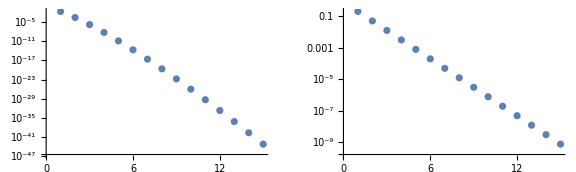

```mathematica
GraphicsRow [{ListLogPlot[puntf/@Range[1,30,2]],ListLogPlot[puntg/@Range[1,30,2]]},ImageSize->Large]
```

Ora si può notare che le due convergenze puntuali hanno lo stesso andamento (esponenziale) e che il seno è significativamente più veloce (la distanza è nell’ordine di  10^-50 dal seno e di 10^-10dalla funzione di Runge 
sviluppando le rispettive approssimazioni fino al 30^oordine)

```mathematica
N[(Log[puntf@2]-Log[puntf@4])/2]
N[(Log[puntg@2]-Log[puntg@4])/2]
```

2.18774

0.693147

## Esercizio 1.2 (Algebra & Coreografie).

#### Testo dell’esercizio:

Le tre radici del polinomio x^3+b x+c dipendono dai coefficienti b e c e sono genericamente complesse (e distinte, ma per speciali valori di b e c una o tutte possono essere reali e due o tutte possono coincidere).
Per ogni scelta di b e c, le radici sono dunque 3 (o 2 o 1) punti nel piano complesso. 
Se si fa muovere il punto (b,c)ϵR^2 lungo una curva Γ in ℝ^2, le radici si muovono lungo tre curve (che possono avere delle intersezioni) nel piano complesso ℂ.
Si chiede di generare un filmato che mostra, affiancati, il moto del punto (b,c) ϵ  ℝ^2 lungo una curva e il corrispondente moto (o `danza’) delle radici in  ℂ.

#### Svolgimento:

Allora, cominciamo dando un nome al nostro polinomio, equivalentemente assegnando una funzione che manda la terna (b,c,x) nel polinomio di terzo grado sopra

```mathematica
P[b_,c_,x_]:= x^3+b x + c
```

```mathematica
rads[a_,b_]:= x/.NSolve[P[a,b,x]==0,x]
```

Una funzione che dati 2 parametri restituisca le radici

```mathematica
C2R2[a_,b_,k_]:= {Re[rads[a,b][[k]]],Im[rads[a,b]][[k]]}
```

```mathematica
pointsRange[a_,b_,range_]:= Graphics[{PointSize[0.02],Red,Point[C2R2[a,b,1]],Green,Point[C2R2[a,b,2]],Blue,Point[C2R2[a,b,3]]},
							PlotRange->{{-range,range},{-range,range}},Axes->True,Ticks->None]
```

Ed una che dati i 2 parametri restituisca i punti come oggetto “Graphics”

```mathematica
dance[t_,a_,b_,γ1_,γ2_]:= GraphicsRow[{Show[
								{ParametricPlot[{γ1[θ],γ2[θ]},{θ,a,b}],
								Graphics[{Purple,PointSize[0.02],Point[{γ1[t],γ2[t]}]}]}
									],
								Show[{
								points[γ1[t],γ2[t]],
								ListLinePlot[Table[C2R2[γ1[τ],γ2[τ],1],{τ,a,t,0.05}],PlotStyle->Red],
								ListLinePlot[Table[C2R2[γ1[τ],γ2[τ],2],{τ,a,t,0.05}],PlotStyle->Green],
								ListLinePlot[Table[C2R2[γ1[τ],γ2[τ],3],{τ,a,t,0.05}],PlotStyle->Blue]
								}]
							}]
```

Una funzione che crea 2 grafici, uno con un punto che si muove sul supporto della curva ed uno con le 3 radici e la “traccia” che lasciano

Nota: ho utilizzato ListLinePlot, avevo fatto un tentativo con ListCurvePathPlot ma in termini di tempi di rendering è decisamente più efficace l’ interpolazione lineare della curva (e graficamente ha la stessa resa)

```mathematica
γ1[t_]:=Cos[t]
γ2[t_] := Sin[t]
points[a_,b_]:= pointsRange[a,b,1.5]
```

Definiamo le componenti di una curva parametrizzata

```mathematica
Manipulate[dance[t,0,2π,γ1,γ2],{t,0,2π}]
```

Il Manipulate è lento ma dà una comoda Preview di come sarà l’animazione poi
Creo una funzione che mi consenta di esportare rapidamente come looping gif a 30fps

```mathematica
exportmygif[list_,name_]:= Export[NotebookDirectory<>name<>".gif",list,ImageSize->Large,"DisplayDurations"->(1/30&/@Range[Length[list]]),"AnimationRepetitions"->∞]
```

e lascio i comandi per esportare la danza sulla circonferenza (animazione di 5 secondi a 30fps)

```mathematica
circleframes = Table[dance[t,0,2π,γ1,γ2],{t,Subdivide[0,2π,150]}];
```

```mathematica
exportmygif[circleframes,circle]
```

mi sembra corretto guardare i risultati della funzione dance anche su un’ellisse.

```mathematica
λ1[t_]:=2Cos[t]
λ2[t_] := Sin[t]
points[a_,b_]:= pointsRange[a,b,2]
```

```mathematica
Manipulate[dance[t,0,2π,λ1,λ2],{t,0,2π}]
```

```mathematica
ellipseframes = Table[dance[t,0,2π,λ1,λ2],{t,Subdivide[0,2π,150]}];
```

```mathematica
exportmygif[ellipseframes,ellipse]
```

### Media 2D:

Ho voluto provare la funzione con curve alcune curve famose, lascio l’immagine finale ed i comandi per esportare in formato .gif
(Ho studiato ulteriormente il caso della cardioide nella sezione “Extra”

#### spirale di Archimede (a=0,b=1):

```mathematica
arcx[t_]:= t Cos[t]
arcy[t_]:=t Sin[t]
points[a_,b_]:= pointsRange[a,b,3]
```

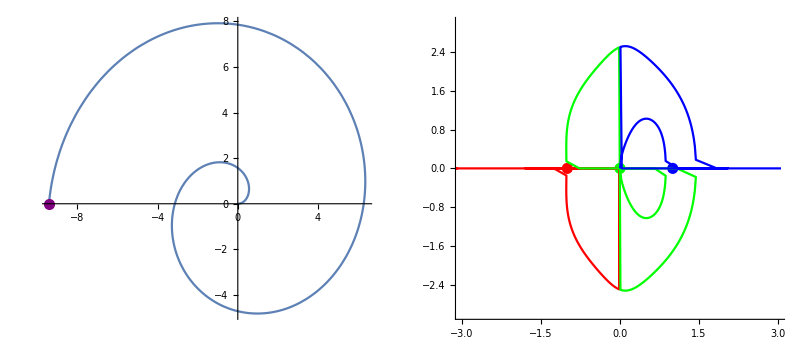

```mathematica
dance[3π,0,3π,arcx,arcy]
```

```mathematica
archiframes = Table[dance[t,0,3π,arcx,arcy],{t,Subdivide[0,3π,150]}];
```

```mathematica
exportmygif[archiframes,archimede]
```

#### Spirale logaritmica (β=1,κ=-1):

```mathematica
logx[t_]:= E^-t Cos[t]
logy[t_]:=E^-t Sin[t]
points[a_,b_]:= pointsRange[a,b,1]
```

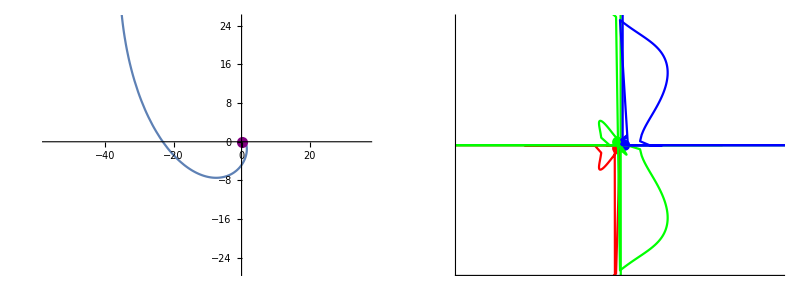

```mathematica
Dance[10,-10,10,logx,logy]
```

```mathematica
logframes = Table[Dance[t,-10,10,logx,logy],{t,Subdivide[-10,10,150]}];
```

```mathematica
exportmygif[logframes,logspiral]
```

#### Cardioide:

```mathematica
cardx[t_]:= Cos[t](1+Cos[t])
cardy[t_]:= Sin[t] (1+Cos[t])
points[a_,b_]:= pointsRange[a,b,1.5]
```

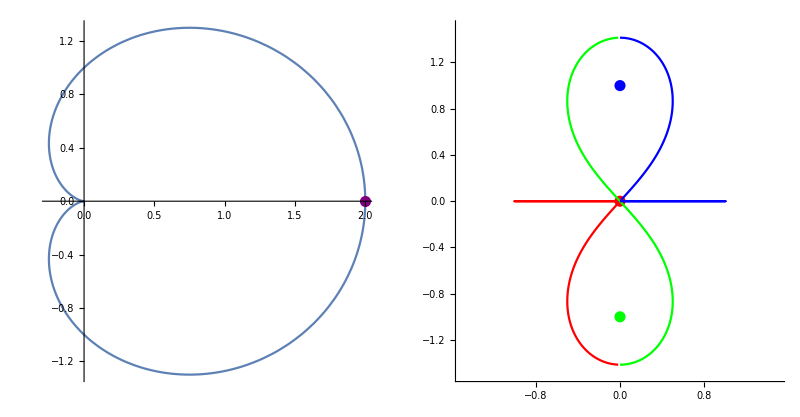

```mathematica
dance[2π,0,2π,cardx,cardy]
```

```mathematica
cardframes = Table[dance[t,0,2π,cardx,cardy],{t,Subdivide[0,2π,150]}];
```

```mathematica
exportmygif[cardframes,cardioid]
```

#### Lemniscata di Bernoulli:

```mathematica
lemx[t_]:= Sin[t]/(1+Cos[t]^2)
lemy[t_]:=(Sin[t]Cos[t])/(1+Cos[t]^2)
points[a_,b_]:= pointsRange[a,b,1.2]
```

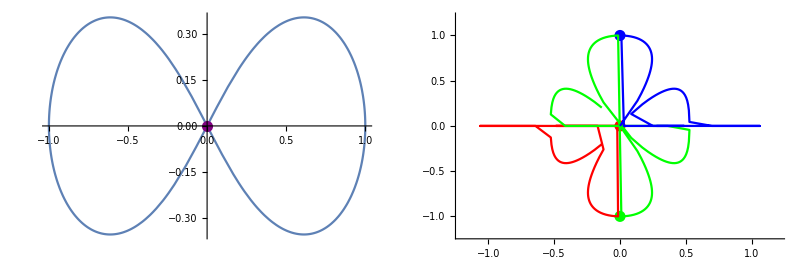

```mathematica
dance[2π,0,2π,lemx,lemy]
```

```mathematica
lemnframes = Table[dance[t,0,2π,lemx,lemy],{t,0,2π,0.05}];
```

```mathematica
exportmygif[lemnframes,lemniscus]
```

#### (pezzo di) Folium di Cartesio:

```mathematica
folx[t_]:= t(t-1)
foly[t_]:=t (t-1)(2t-1)
points[a_,b_]:= pointsRange[a,b,1]
```

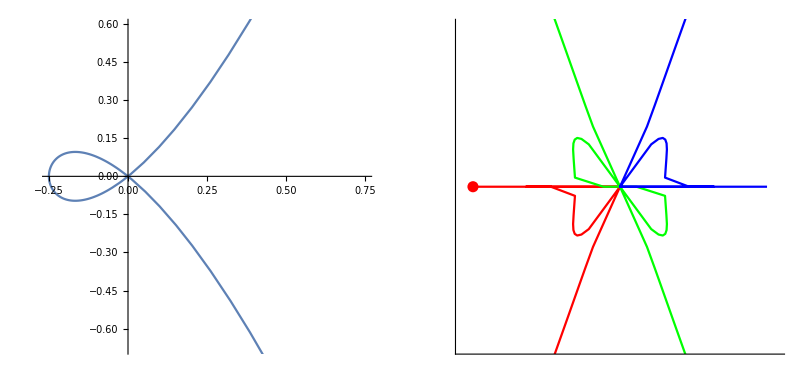

```mathematica
dance[1.5,-0.5,1.5,folx,foly]
```

```mathematica
foliumframes = Table[dance[t,-0.5,1.5,folx,foly],{t,Subdivide[-0.5,1.5,150]}];
```

```mathematica
exportmygif[foliumframes,folium]
```

### Extra (Cardioidi e Lemniscate):

Il fatto che la cardioide producesse qualcosa di simile alla lemniscata mi ha incuriosito; 
riportiamo la parametrizzazione.

```mathematica
cardx[t_]:= Cos[t](1+Cos[t])
cardy[t_]:= Sin[t] (1+Cos[t])
points[a_,b_]:= pointsRange[a,b,1.5]
```

Creiamo il grafico solo della parte che ci interessa

```mathematica
lemnimaybe =Show[{ListLinePlot[Table[C2R2[cardx[τ],cardy[τ],1],{τ,0,2π,0.05}],PlotStyle->Red,PlotRange->{{-1,1},{-1.5,1.5}}],
			ListLinePlot[Table[C2R2[cardx[τ],cardy[τ],2],{τ,0,2π,0.05}],PlotStyle->Green,PlotRange->{{-1,1},{-1.5,1.5}}],
			ListLinePlot[Table[C2R2[cardx[τ],cardy[τ],3],{τ,0,2π,0.05}],PlotStyle->Blue,PlotRange->{{-1,1},{-1.5,1.5}}]}]
```

Cerco di capire quale sia la scala della figura (dove stanno i massimi ed i minimi), posso cercare il massimo delle due coordinate dell punto verde al variare di t

```mathematica
Max[Table[C2R2[cardx[τ],cardy[τ],2][[1]],{τ,0,2π,0.01}]]
Max[Table[C2R2[cardx[τ],cardy[τ],2][[2]],{τ,0,2π,0.01}]]
```

Congetturo che La scala sia di 1/2 nella direzione dell’asse x e di √2nella direzione dell’asse y

```mathematica
Lemn = ParametricPlot[{1/2(1+Cos[1]^2)/(Cos[1]Sin[1])(Sin[t]Cos[t])/(1+Cos[t]^2),√2 Sin[t]/(1+Cos[t]^2)},{t,0,2π},PlotStyle->{Purple,Dashed,Thick}];
```

```mathematica
Max[Table[(Sin[t]Cos[t])/(1+Cos[t]^2),{t,0,2π}]]
```

Scalo opportunamente la lemniscata e
controlliamo se si sovrappongono

```mathematica
Show[{lemnimaybe,Lemn},ImageSize-> Large]
```

Sembrano sovrapporsi, cercherò di dimostrare questo fatto:
Vogliamo dimostrare che Supp (ℒ) ⊆ (∪^3)_(k=1)Supp(x_k(t)) ,dove ℒ è la Lemniscata di Bernoulli opportunamente scalata e x_1 x_2 e x_3 sono le 3 radici di x^3+a(t)x+b(t), dove a(t)e b(t) variano sulla cardioide

Questo è verificato solo se, posto z(t*)=lemnx(t*)+ 𝒾 lemny(t*)
z(t^*)^3+a(t)z(t^*)+b(t) == 0 ha soluzione ∀t*∈[0,2π] ∃ t ∈[0,2π]

```mathematica
Pcard[t_,x_]:= Norm[P[Cos[t](1+Cos[t]),Sin[t] (1+Cos[t]),x]]
```

```mathematica
cmplxL[t_]:= 1/2(1+Cos[1]^2)/(Cos[1]Sin[1])(Sin[t]Cos[t])/(1+Cos[t]^2)+ I √2 Sin[t]/(1+Cos[t]^2)
```

```mathematica
Manipulate[Plot[Pcard[t,cmplxL[τ]],{t,0,2π},PlotRange->{0,1.5}],{τ,0,2π}]
```

Facendo variare τ si ha che ogni funzione generata ha almeno uno 0 (con le dovute approssimazioni dovute alla limitata precisione delle funzioni e all’approssimazione “a occhio” della parametrizzazione della lemniscata modificata)

La prova non è rigorosa nè particolarmente elegante, tuttavia permette di congetturare la correttezza di un risultato simile (ossia riscalando più accuratamente la lemniscata)

### Generalizzazione a curve in ℝ^3 :

Viene naturale porsi il medesimo problema sul polinomio x^3+ax^2+bx+c con a,b,c che variano lungo una curva in R^3
Gli step sono i medesimi:

```mathematica
P[a_,b_,c_,x_]:= x^3+a x^2+b x + c
```

```mathematica
rads[a_,b_,c_]:= x/.NSolve[P[a,b,c,x]]
```

```mathematica
c2r2[a_,b_,c_,k_]:= {Re[rads[a,b,c][[k]]],Im[rads[a,b,c]][[k]]}
```

```mathematica
pointsRange[a_,b_,c_,range_]:= Graphics[{PointSize[0.02],
														Red,Point[c2r2[a,b,c,1]],
														Green,Point[c2r2[a,b,c,2]],
														Blue,Point[c2r2[a,b,c,3]]},
							PlotRange->{{-range,range},{-range,range}},Axes->True,Ticks->None]
```

```mathematica
dance3D[t_,a_,b_,i_,j_,k_]:= GraphicsRow[{Show[
								{ParametricPlot3D[{i[θ],j[θ],k[θ]},{θ,a,b}],
								Graphics3D[{Purple,PointSize[0.02],Point[{i[t],j[t],k[t]}]}]}
									],
								Show[{
								points[i[t],j[t],k[t]]
								,ListLinePlot[Table[c2r2[i[τ],j[τ],k[τ],1],{τ,a,t,0.025}],PlotStyle->Red],
								ListLinePlot[Table[c2r2[i[τ],j[τ],k[τ],2],{τ,a,t,0.025}],PlotStyle->Green],
								ListLinePlot[Table[c2r2[i[τ],j[τ],k[τ],3],{τ,a,t,0.025}],PlotStyle->Blue]
								}]
							},ImageSize->Large]
```

```mathematica
i[t_]:= Cos[t]
j[t_]:= Sin[t]
k[t_]:= t
points[a_,b_,c_]:= pointsRange[a,b,c,4]
```

Provo con un’Elicoide in un quadrato 6x6

```mathematica
Manipulate[dance3D[t,0,4π,i,j,k],{t,0,4π}]
```

E questo è quanto, nulla di troppo diverso dalla versione 2D.
Tuttavia ci porta alla possibilità di crearne di nuove (sezione Media3D)

```mathematica
elicoidframes = Table[dance3D[t,0,4π,i,j,k],{t,Subdivide[0,4π,150]}];
```

```mathematica
exportmygif[elicoidframes,elicoid]
```

### Media 3D:

Messa a punto la funzione in 3D lascio immagini e comandi come sopra per alcune curve 3D famose

#### (pezzo di) Nodo di LissaJous (a,b,c,ϕ,ψ,n=1,m=2):

```mathematica
lisx[t_]:= Sin[t]
lisy[t_]:= Sin[t+1]
lisz[t_]:= Sin[2t+1]
points[a_,b_,c_]:= pointsRange[a,b,c,1.5]
```

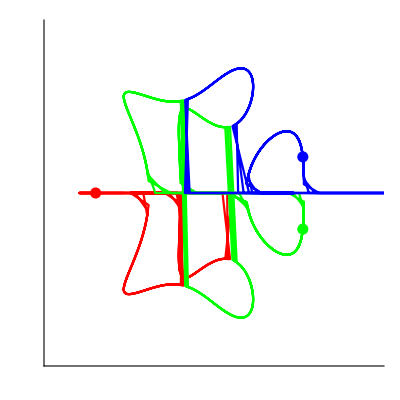

```mathematica
dance3D[10,-10,10,lisx,lisy,lisz]
```

```mathematica
lissaframes = Table[dance3D[t,-10,10,lisx,lisy,lisz],{t,Subdivide[-10,10,150]}];
```

```mathematica
exportmygif[lissaframes,lissajous]
```

#### Bordo della finestra di Viviani:

```mathematica
vivx[t_]:= 1+Cos[t]
vivy[t_]:= Sin[t]
vivz[t_]:= 2Sin[t/2]
points[a_,b_,c_]:= pointsRange[a,b,c,1.5]
```

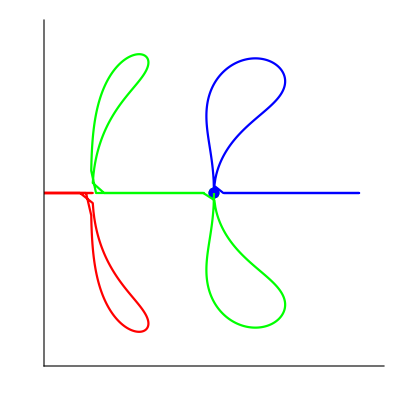

```mathematica
dance3D[4π,0,4π,vivx,vivy,vivz]
```

```mathematica
vivianframes = Table[dance3D[t,0,4π,vivx,vivy,vivz],{t,Subdivide[0,4π,150]}];
```

```mathematica
exportmygif[vivianframes,viviani]
```

#### Cucitura di una palla da tennis (a,b,c=1):

```mathematica
tenx[t_]:= Cos[t]+Cos[3t]
teny[t_]:= Sin[t]-Sin[3t]
tenz[t_]:= Sin[2t]
points[a_,b_,c_]:= pointsRange[a,b,c,1.5]
```

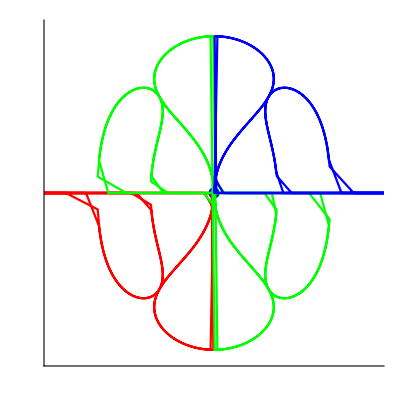

```mathematica
dance3D[4π,0,4π,tenx,teny,tenz]
```

```mathematica
tennisframes = Table[dance3D[t,0,4π,tenx,teny,tenz],{t,Subdivide[0,4π,150]}];
```

```mathematica
exportmygif[tennisframes,tennisball]
```

## Esercizio 1.3 (Teorema dei numeri primi).

#### Testo dell’esercizio:

Il teorema dei numeri primi afferma che le funzioni    π(n)   ,   n/log(n)  ,   li(n)   sono asintotiche per   n→∞ .
Investigare numericamente questa affermazione.

### Svolgimento:

## Esercizio 1.4 (Catenaria).

### Testo dell’esercizio:

Se, nel piano xy, un cerchio di raggio r rotola senza strisciare sull’asse x, un punto P del cerchio descrive, nel piano xy, una curva chiamata catenaria, di equazioni parametriche
   t → (rt - r sin(t) , r - r cos(t) )
Produrre un’animazione (e magari un filmato) che mostra il cerchio (o un disco) che  rotola, il punto P su di essa, e la curva descritta da P nel piano

### Svolgimento: